```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../setup.nb"]
```

```mathematica
abortOnMessageOn[]
```

Load pre-processed data

```mathematica
Get[NotebookDirectory[]<>"../../Data/WT/mesh-data.mx"]
```

## Length and tension dynamics during T1s

### Edge collapses (Fig. 2D,E; left half of the plots)

#### Germ band

```mathematica
persistentCollapsesGermBand=With[{nonDorsal=Complement[bodyCells,dvStratifiedBodyCells[[7]],dvStratifiedBodyCells[[8]]]},
KeySelect[persistentCollapses,MemberQ[nonDorsal,#[[1]]]&&MemberQ[nonDorsal,#[[2]]]&]];
```

Length

```mathematica
edgeLengthData=KeyValueMap[
Table[{t-#2+1,sharedEdgeLength[#1,t]},{t,#2-1}]&,
Select[persistentCollapsesGermBand,#>50&]
];//AbsoluteTiming
```

{4.02501,Null}

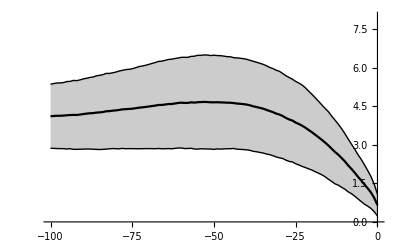

```mathematica
collapseLengthPlot=Show[
ListLinePlot[{
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[Catenate[edgeLengthData]],#[[1]]>=-100&]
},
IntervalMarkers->"Bands",
PlotRange->{0,8},
PlotStyle->Black
]
]
```

Inferred tensions

```mathematica
edgeTensionData=Association[KeyValueMap[#1->Table[
{t-#2+1,If[MissingQ[#],#,{
#,
quartetEdgeTension[#[[4]]]
}]&@edgeNeighborProperties[#1,t]},
{t,1,#2-1}]&,
Select[persistentCollapsesGermBand,#>50&]
]];//AbsoluteTiming
```

{62.5006,Null}

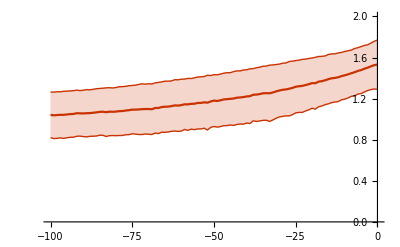

```mathematica
collapseTensionPlot=With[{
(* filter out very short edges (< 0.75 µm length) and missing data *)
data=({#[[1]],#[[2,2]]}&/@Select[#,!MissingQ[#[[2]]]&&0<#[[2,2]]<2&&Min[#[[2,1,3,2;;-1]]]>0.75&])&/@Values[edgeTensionData]},
ListLinePlot[{
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[Catenate[data]],#[[1]]>=-100&]
},
IntervalMarkers->"Bands",
PlotRange->{0,2},
PlotStyle->ColorData[112,1]
]
]
```

#### Amnioserosa (dorsal pole)

```mathematica
persistentCollapsesDorsal=KeySelect[persistentCollapses,MemberQ[bodyCellsDorsal,#[[1]]]||MemberQ[bodyCellsDorsal,#[[2]]]&];
```

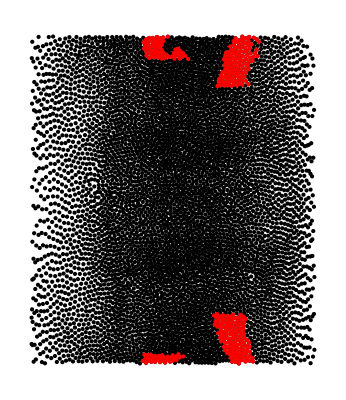

```mathematica
With[{t=1},Graphics[{
Point[toCylinder/@Values[cellCentroidsTS[[t]]]],
Red,
If[!MissingQ[#],Point[toCylinder[#]]]&@cellCentroidsTS[[t]][#]&/@amnioserosaCells
}]]
```

```mathematica
edgeLengthDataDorsal=KeyValueMap[
Table[{t-#2+1,sharedEdgeLength[#1,t]},{t,#2-1}]&,
Select[persistentCollapsesDorsal,50<#&]
];//AbsoluteTiming
```

{0.266026,Null}

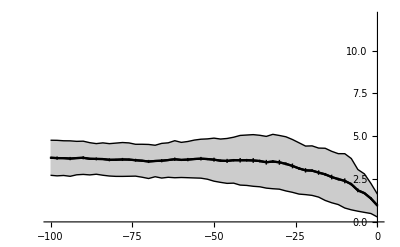

```mathematica
collapseLengthPlotDorsal=
ListLinePlot[{
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[Catenate[edgeLengthDataDorsal],2],#[[1]]>=-100&&Length[#[[2]]]>10&],
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]/√Length[#[[2]]]]}&/@Select[binByFirst[Catenate[edgeLengthDataDorsal],2],#[[1]]>=-100&&Length[#[[2]]]>10&]
},
IntervalMarkers->{"Bands","Fences"},
PlotRange->{0,12},
PlotStyle->Black
]
```

```mathematica
edgeTensionDataDorsal=Association[KeyValueMap[#1->Table[
{t-#2+1,If[MissingQ[#],#,{
#,
quartetEdgeTension[#[[4]]]
}]&@edgeNeighborProperties[#1,t]},
{t,1,#2-1}]&,
Select[persistentCollapsesDorsal,#>50&]
]];//AbsoluteTiming
```

{3.128,Null}

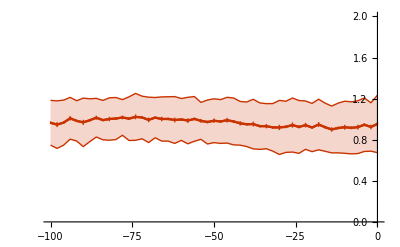

```mathematica
collapseTensionPlotDorsal=With[{
(* filter out very short edges (< 0.75 µm length) and missing data *)
tensionData=binByFirst[Catenate[
({#[[1]],Clip[#[[2,2]],{0,2}]}&/@Select[#,!MissingQ[#[[2]]]&&0<#[[2,2]]<2&&Min[#[[2,1,3,2;;-1]]]>0.75&])&/@Values[edgeTensionDataDorsal]],2]},
ListLinePlot[{
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[tensionData,#[[1]]>=-100&&Length[#[[2]]]>10&],
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]/√Length[#[[2]]]]}&/@Select[tensionData,#[[1]]>=-100&&Length[#[[2]]]>10&]
},
IntervalMarkers->{"Bands","Fences"},
PlotRange->{0,2},
PlotStyle->ColorData[112,1]
]
]
```

### New edges (Fig. 2D,E; right half of the plots)

```mathematica
edgeCreationEventsRaw=KeySelect[
Association[
First@Last@Reap[KeyValueMap[
Function[{pair,ts},
With[{trunc=dropTrailingMissingCells[ts]},
If[Max[trunc[[1;;Min[50,Length[trunc]]]]]==0&&trunc[[-1]]==1,
If[#!=0,Sow[pair->#+1]]&@lastPosition[trunc,0]
]]
],
pairContactTS
]]
],
Not[MemberQ[invaginatingCells,#[[1]]]||MemberQ[invaginatingCells,#[[2]]]]&
];//AbsoluteTiming
```

{1.2159,Null}

Filter out edge creations due to invaginations by checking if the shortest path between the cells passes through an invaginating cell at the first timepoint.

```mathematica
initGraph=makeGraph[Keys[cellNeighborsTS[[1]]],cellNeighborsTS[[1]]];
```

```mathematica
checkInvagination[pair_]:=If[
KeyExistsQ[cellCentroidsTS[[1]],pair[[1]]]&&KeyExistsQ[cellCentroidsTS[[1]],pair[[2]]],
Length[Intersection[FindShortestPath[initGraph,pair[[1]],pair[[2]]],invaginatingCells]]>0,
True
]
```

```mathematica
edgeCreationEvents=KeySelect[
edgeCreationEventsRaw,
Association[KeyValueMap[
#1->!checkInvagination[#1]&,
edgeCreationEventsRaw
]]
];//AbsoluteTiming
```

{2.20923,Null}

Timing of edge creation events.

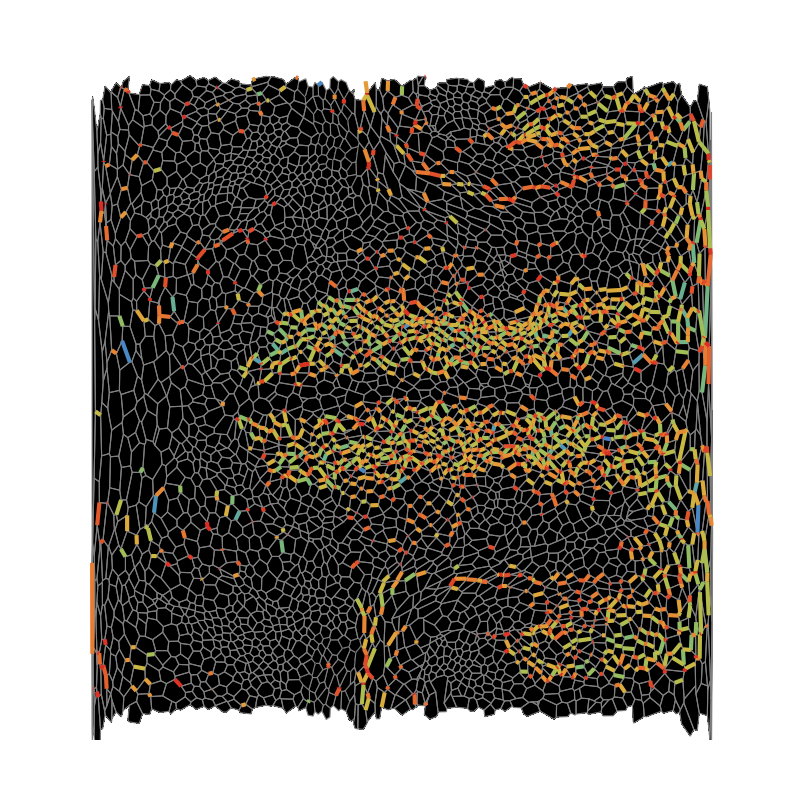

```mathematica
Graphics[{
EdgeForm[Gray],FaceForm[Black],
Tooltip[renderCell2D[#,-1],#]&/@Keys[cellCentroidsTS[[-1]]],
AbsoluteThickness[3],CapForm["Butt"],
Map[
Function[event,{ColorData["Rainbow"][event[[2]]/200],renderSharedEdge[event[[1]],-1]}],
SortBy[Normal[edgeCreationEvents],Last]
]
},
AspectRatio->1,
PlotRange->{{0,510},{-20,560}},
ImageSize->800
]
```

#### Germ band

```mathematica
edgeCreationEventsGermBand=With[{nonDorsal=Complement[bodyCells,bodyCellsDorsal]},
KeySelect[edgeCreationEvents,MemberQ[nonDorsal,#[[1]]]&&MemberQ[nonDorsal,#[[2]]]&]];
```

```mathematica
Length[Select[edgeCreationEventsGermBand,#>50&]]
```

2413

Length

```mathematica
newEdgeLengthData=KeyValueMap[
DeleteCases[Table[{t-#2+1,sharedEdgeLength[#1,t]},{t,#2,198}],{_,0}]&,
Select[edgeCreationEventsGermBand,#>50&]
];//AbsoluteTiming
```

{1.34136,Null}

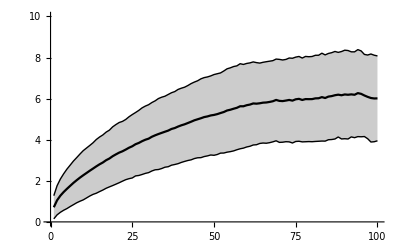

```mathematica
newEdgeLengthPlot=Show[
ListLinePlot[{
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[Catenate[newEdgeLengthData]],#[[1]]<=100&&Length[#[[2]]]>5&]
},
IntervalMarkers->"Bands",
PlotRange->{{0,100},{0,10}},
PlotStyle->Black
]
]
```

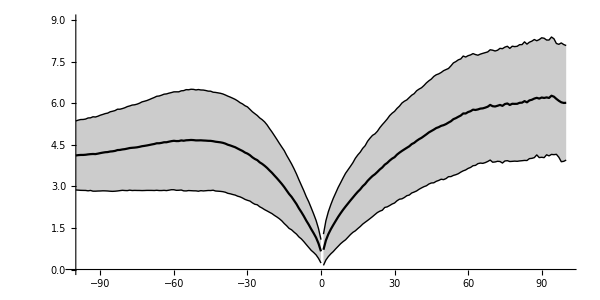

```mathematica
Show[collapseLengthPlot,newEdgeLengthPlot,PlotRange->{{-100,100},{0,9}},ImageSize->600,AspectRatio->1/2,AxesOrigin->{-100,0}]
```

Tension

```mathematica
newEdgeTensionData=Association[KeyValueMap[#1->Table[
{t-#2+1,If[MissingQ[#],#,{
#,
quartetEdgeTension[#[[4]]]
}]&@edgeNeighborProperties[#1,t]},
{t,#2,198}]&,
Select[edgeCreationEventsGermBand,#>50&]
]];//AbsoluteTiming
```

{16.6664,Null}

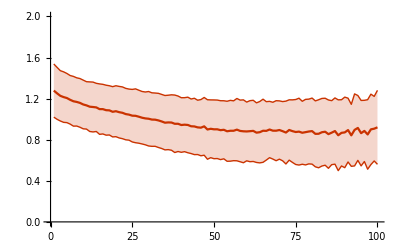

```mathematica
newEdgeTensionPlot=With[{
tensionData=binByFirst@Catenate[
(* Filter very short edges and missing data, clip range of relative tension to physical range [0,2] *)
({#[[1]],Clip[#[[2,2]],{0,2}]}&/@Select[#,!MissingQ[#[[2]]]&&0<#[[2,2]]<2&&Min[#[[2,1,3,2;;-1]]]>0.75&])&/@Values[newEdgeTensionData]]},
ListLinePlot[{
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[tensionData,#[[1]]<=100&&Length[#[[2]]]>5&]
},
IntervalMarkers->"Bands",
PlotRange->{0,2},
PlotStyle->ColorData[112,1]
]
]
```

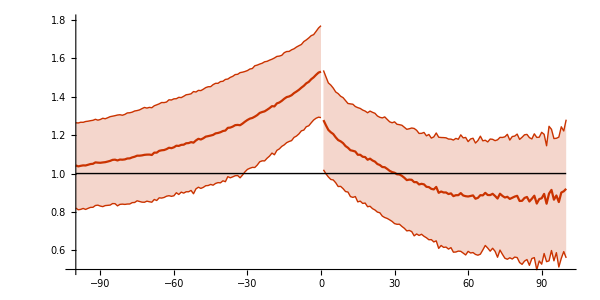

```mathematica
Show[collapseTensionPlot,newEdgeTensionPlot,Graphics[Line[{{-100,1},{100,1}}]],PlotRange->{{-100,100},{0.5,1.8}},ImageSize->600,AspectRatio->1/2,
AxesOrigin->{-100,0.5}]
```

#### Amnioserosa (dorsal pole)

```mathematica
edgeCreationEventsDorsal=With[{nonDorsal=Complement[bodyCellsDorsal,bodyCellsDorsal]},
KeySelect[edgeCreationEvents,MemberQ[bodyCellsDorsal,#[[1]]]&&MemberQ[bodyCellsDorsal,#[[2]]]&]];
```

```mathematica
newEdgeLengthDataDorsal=KeyValueMap[
DeleteCases[Table[{t-#2+1,sharedEdgeLength[#1,t]},{t,#2,198}],{_,0}]&,
Select[edgeCreationEventsDorsal,#>50&]
];//AbsoluteTiming
```

{0.049985,Null}

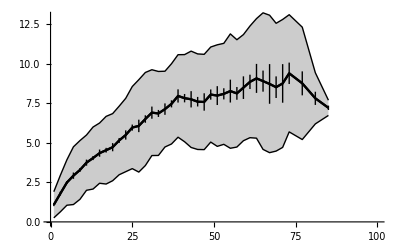

```mathematica
newEdgeLengthPlotDorsal=
ListLinePlot[{
{#[[1]]+1,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[binByFirst[Catenate[newEdgeLengthDataDorsal],2],#[[1]]<=100&&Length[#[[2]]]>10&],
{#[[1]]+1,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]/√Length[#[[2]]]]}&/@Select[binByFirst[Catenate[newEdgeLengthDataDorsal],2],#[[1]]<=100&&Length[#[[2]]]>10&]
},
IntervalMarkers->{"Bands","Fences"},
PlotRange->{{0,100},{0,13}},
PlotStyle->Black
]
```

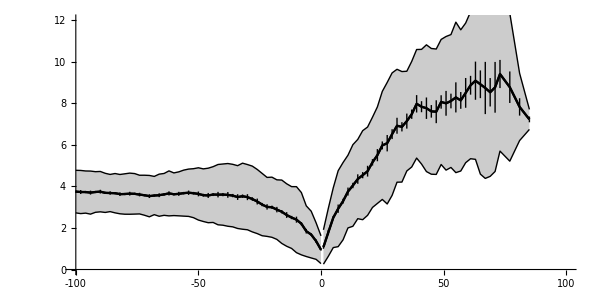

```mathematica
Show[collapseLengthPlotDorsal,newEdgeLengthPlotDorsal,
PlotTheme->"PDFExport",
PlotRange->{{-100,100},{0,12}},PlotRangePadding->None,
ImageSize->600,AspectRatio->1/2,
AxesOrigin->{-100,0},
Ticks->{Range[-100,100,50],Range[0,12,2]}
]
```

```mathematica
newEdgeTensionDataDorsal=Association[KeyValueMap[#1->Table[
{t-#2+1,If[MissingQ[#],#,{
#,
quartetEdgeTension[#[[4]]]
}]&@edgeNeighborProperties[#1,t]},
{t,#2,198}]&,
Select[edgeCreationEventsDorsal,#>50&]
]];//AbsoluteTiming
```

{0.988436,Null}

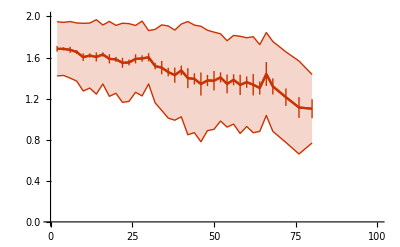

```mathematica
newEdgeTensionPlotDorsal=With[{
tensionData=binByFirst[Catenate[
({#[[1]]+1,Clip[#[[2,2]],{0,2}]}&/@Select[#,!MissingQ[#[[2]]]&&0<#[[2,2]]<2&&Min[#[[2,1,3,2;;-1]]]>0.75&])&/@Values[newEdgeTensionDataDorsal]],2]},
ListLinePlot[{
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[tensionData,#[[1]]<=100&&Length[#[[2]]]>10&],
{#[[1]],Around[Mean[#[[2]]],StandardDeviation[#[[2]]]/√Length[#[[2]]]]}&/@Select[tensionData,#[[1]]<=100&&Length[#[[2]]]>10&]
},
IntervalMarkers->{"Bands","Fences"},
PlotStyle->ColorData[112,1],
PlotRange->{{0,100},{0,2}}
]
]
```

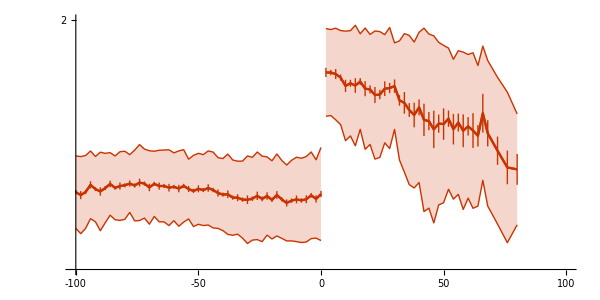

```mathematica
Show[collapseTensionPlotDorsal,newEdgeTensionPlotDorsal,
PlotRange->{{-100,100},{0.5,2}},PlotRangePadding->None,
ImageSize->600,
AspectRatio->1/2,
AxesOrigin->{-100,0.5},
Ticks->{Range[-100,100,50],Range[0,12,2]}
]
```

### Stripe-resolved analysis (Fig. 2S1)

```mathematica
getEdgeTensionData[edge:{_Integer,_Integer},t_Integer]:=With[{
props=edgeNeighborProperties[edge,t]
},
If[MissingQ[props],
props,(* Pass on missing object *)
{
props,
quartetEdgeTensions[props[[4]]]
}]
]
```

```mathematica
edgeCollapseStripeData=Table[
Association[KeyValueMap[
Function[{edge,t0},edge->Table[
{t-t0+1,getEdgeTensionData[edge,t]},
{t,1,t0-1}]],
Select[KeySelect[persistentCollapses,Length[Intersection[#,stripeCells]]>0&],#>50&]
]],
{stripeCells,dvStratifiedBodyCells}
];//AbsoluteTiming
```

{73.4858,Null}

```mathematica
edgeCreationStripeData=Table[
Association[KeyValueMap[
Function[{edge,t0},edge->Table[
{t-t0+1,getEdgeTensionData[edge,t]},
{t,t0,198}]],
Select[KeySelect[edgeCreationEvents,Length[Intersection[#,stripeCells]]>0&],#>50&]
]],
{stripeCells,dvStratifiedBodyCells}
];//AbsoluteTiming
```

{26.9484,Null}

Filter very short edges (< 0.75 µm) and missing data

```mathematica
filterTensionData[data_]:={#[[1]],#[[2,2,1]]}&/@Select[data,!MissingQ[#[[2]]]&&0<#[[2,2,1]]<2&&Min[#[[2,1,3,2;;-1]]]>0.75&]
```

```mathematica
Length/@edgeCollapseStripeData
```

{368,635,557,512,311,152,90,115}

```mathematica
Length/@edgeCreationStripeData
```

{444,846,783,700,461,222,105,102}

```mathematica
tensionPlots=Table[
withOuterTicks[ListLinePlot[{
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[
binByFirst@Catenate[filterTensionData/@Values[edgeCollapseStripeData[[stripeIndex]]]],
Length[#[[2]]]>10&&-100<=#[[1]]&
],
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[
binByFirst@Catenate[filterTensionData/@Values[edgeCreationStripeData[[stripeIndex]]]],
Length[#[[2]]]>10&&#[[1]]<=100&
]
},
PlotStyle->ColorData["Rainbow"][(stripeIndex-1)/7],
IntervalMarkers->"Bands",IntervalMarkersStyle->{"LineOpacity"->0},
PlotRange->{{-25,25},{0.5,2}},
PlotRangeClipping->False,
Axes->False,
FrameTicks->{{Range[0.5,2,0.5],{}},{Range[-25,25,25],{}}},
Frame->True,
PlotTheme->"PDFExport",
ImageSize->200,ImagePadding->{{30,10},{25,10}}
],6],
{stripeIndex,8}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Do[
Export["/Users/Fridtjof.Brauns/KITP/GBE/Figures/Quartet Analysis/edge-tension_stripe-"<>IntegerString[i]<>".pdf",tensionPlots[[i]]],
{i,Length[tensionPlots]}
]
```

Filter very short edges (< 0.75 µm) and missing data

```mathematica
filterLengthData[data_]:={#[[1]],#[[2,1,3,1]]}&/@Select[data,!MissingQ[#[[2]]]&&0<#[[2,2,1]]<2&&Min[#[[2,1,3,2;;-1]]]>0.75&]
```

```mathematica
lengthPlots=Table[
withOuterTicks[ListLinePlot[{
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[
binByFirst@Catenate[filterLengthData/@Values[edgeCollapseStripeData[[stripeIndex]]]],
Length[#[[2]]]>10&&-100<=#[[1]]&
],
{#[[1]]/4,Around[Mean[#[[2]]],StandardDeviation[#[[2]]]]}&/@Select[
binByFirst@Catenate[filterLengthData/@Values[edgeCreationStripeData[[stripeIndex]]]],
Length[#[[2]]]>10&&#[[1]]<=100&
]
},
PlotStyle->ColorData["Rainbow"][(stripeIndex-1)/7],
IntervalMarkers->"Bands",IntervalMarkersStyle->{"LineOpacity"->0},
PlotRange->{{-25,25},{0,12}},
PlotRangeClipping->False,
Axes->False,
FrameTicks->{{Range[0,12,2],{}},{Range[-25,25,25],{}}},
Frame->True,
PlotTheme->"PDFExport",
ImageSize->200,ImagePadding->{{30,10},{25,10}}
],6],
{stripeIndex,8}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Do[
Export["/Users/Fridtjof.Brauns/KITP/GBE/Figures/Quartet Analysis/edge-length_stripe-"<>IntegerString[i]<>".pdf",lengthPlots[[i]]],
{i,Length[lengthPlots]}
]
```

### Correlation between edge tension and collapse time

```mathematica
edgeTension[cellPair_,t_]:=If[
MissingQ[#],#,
(*Clip[quartetEdgeTension[#[[4]]],{0,2}]*)
If[0<=#<=2,#,Missing["DegenerateEdge",cellPair]]&@quartetEdgeTension[#[[4]]]
]&@edgeNeighborProperties[cellPair,t]
```

#### Persistently collapsing edges

```mathematica
persistentCollapsesBody=KeySelect[
(Last/@SequencePosition[#,{1,0}])&/@Select[pairContactTS,
With[{l=dropTrailingMissingCells[#]},
l[[1]]==1&&l[[-1]]==0
]&
],
MemberQ[bodyCells,#[[1]]]&&MemberQ[bodyCells,#[[2]]]&
];
```

```mathematica
tensionCollapseTimeStratified=Module[{
ts=1+4 20,te=1+4 21,
pairs
},
Map[Function[{cells},
pairs=Select[
Select[Keys[persistentCollapsesBody],MemberQ[cells,#[[1]]]&&MemberQ[cells,#[[2]]]&],
pairContactTS[#][[ts;;te]]==ConstantArray[1,te-ts+1]&
];
{
If[#=!={},Mean[#],0]&@DeleteMissing[Table[edgeTension[#,t],{t,ts,te}]],
SelectFirst[persistentCollapsesBody[#]-te,#>0&,-1]
}&/@pairs
],
dvStratifiedBodyCells
]
];//AbsoluteTiming
```

{2.54332,Null}

Germ band

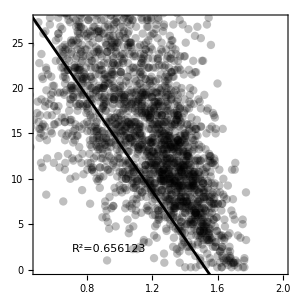

```mathematica
With[{fit=LinearModelFit[
{#[[1]],#[[2]]/4}&/@Catenate[tensionCollapseTimeStratified[[1;;6]]],
{(x-1.53)},x,
(*Weights->Clip[Catenate[tensionCollapseTimeStratified[[1;;6,All,1]]]-1,{0,2}],*)
IncludeConstantBasis->False
]},
Show[
Graphics[{
Black,
AbsolutePointSize[6],
Opacity[0.25],
Point[{#[[1]],#[[2]]/4}&/@Select[Catenate[tensionCollapseTimeStratified[[1;;6]]],#[[2]]>0&]]
},
PlotRange->{{0.5,2},{0,110/4}},
AspectRatio->1,
PlotRangeClipping->True,
Frame->True,
ImageSize->300,
Background->White
],
Plot[Normal[fit],{x,0,2},
PlotStyle->Directive[Black,AbsoluteThickness[2]],
PlotLegends->Placed["R^2="<>ToString[fit["RSquared"]],{0.3,0.1}]
]]
]
```

Amnioserosa

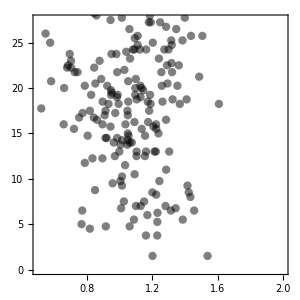

```mathematica
Graphics[{
Black,
AbsolutePointSize[6],
Opacity[0.5],
Point[{#[[1]],#[[2]]/4}&/@Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],#[[2]]>0&]]
},
PlotRange->{{0.5,2},{0,110/4}},
AspectRatio->1,
PlotRangeClipping->True,
Frame->True,
ImageSize->300,
Background->White
]
```

```mathematica
Correlation@@Transpose[Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],0<#[[1]]<2&&#[[2]]>0&]]
```

-0.180725

```mathematica
Length[Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],#[[2]]>0&]]
```

179

Resolved by DV position

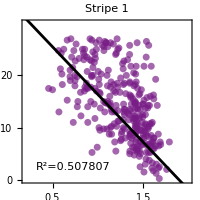
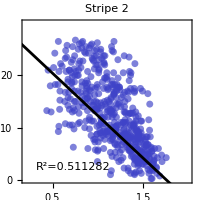
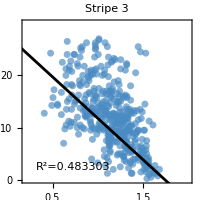
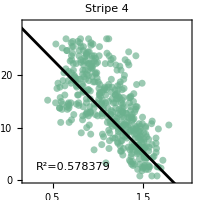
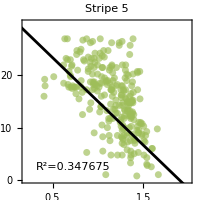
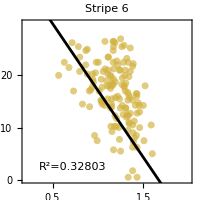
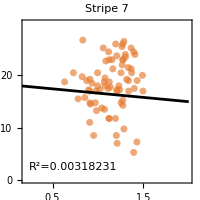
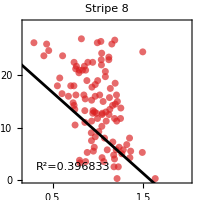

```mathematica
Row[Table[
With[{fit=LinearModelFit[
{#[[1]],#[[2]]/4}&/@tensionCollapseTimeStratified[[i]],
{1,x},x,
Weights->1/tensionCollapseTimeStratified[[i,All,2]]
]},
Show[
Graphics[{
Opacity[0.67],dvStripeColors[[i]],
AbsolutePointSize[5],
Point[{#[[1]],#[[2]]/4}&/@Select[tensionCollapseTimeStratified[[i]],#[[2]]>0&]]
},
PlotRange->{{0.2,2},{0,120/4}},AspectRatio->1,
PlotRangeClipping->True,
Frame->True,FrameTicks->{{Range[0,25,5],None},{Range[0.5,2,0.5],None}},
PlotLabel->"Stripe "<>ToString[i],
ImageSize->200
],
Plot[Normal[fit],{x,0,2},
PlotStyle->Directive[Black,AbsoluteThickness[2]],
PlotLegends->Placed["R^2="<>ToString[fit["RSquared"]],{0.3,0.1}]
]
]
],
{i,Length[dvStratifiedBodyCells]}
]]
```

Some improvement might be possible by averaging vertex positions before calculating relative tension.

```mathematica
permanentEdgeTensions=Mean[DeleteMissing[Table[edgeTension[#,t],{t,81,85}]]]&/@permanentPairs;
```

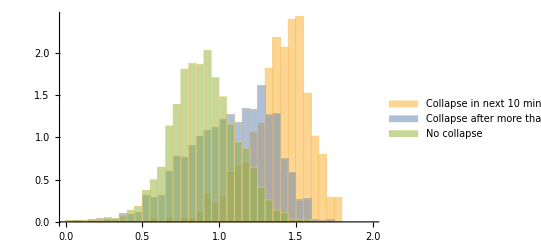

```mathematica
Histogram[{
Select[Catenate[tensionCollapseTimeStratified[[1;;6]]],0<#[[2]]<4 10&][[All,1]],
Select[Catenate[tensionCollapseTimeStratified[[1;;6]]],#[[2]]>4 10&][[All,1]],
permanentEdgeTensions
},
{0,2,0.05},
"PDF",
ChartLegends->{"Collapse in next 10 min","Collapse after more than 10 min","No collapse"}
]
```

```mathematica
Length[Catenate[tensionCollapseTimeStratified[[1;;6]]]]
```

2061

```mathematica
Length/@{
Select[permanentEdgeTensions,0<#<2&],
Select[Catenate[tensionCollapseTimeStratified[[1;;6]]],#[[2]]>=4 10&][[All,1]],
Select[Catenate[tensionCollapseTimeStratified[[1;;6]]],0<#[[2]]<4 10&][[All,1]]
}
```

{5482,1509,552}

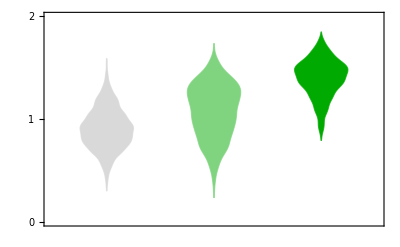

```mathematica
DistributionChart[{
Select[permanentEdgeTensions,0<#<2&],
Select[Catenate[tensionCollapseTimeStratified[[1;;6]]],#[[2]]>4 10&][[All,1]],
Select[Catenate[tensionCollapseTimeStratified[[1;;6]]],0<#[[2]]<4 10&][[All,1]]
},
PlotRange->{0,2},
FrameTicks->{{{0,1,2},None},None},
ChartStyle->{LightGray,Blend[{Darker[Green],White},0.5],Darker[Green]}
]
```

```mathematica
LocationTest[{
Select[permanentEdgeTensions,0<#<2&],
Select[Catenate[tensionCollapseTimeStratified[[1;;6]]],0<#[[1]]<2&&#[[2]]>4 10&][[All,1]]
},
0,
"T",
VerifyTestAssumptions->"EqualVariance"]
```

5.43412×10^-100

Amnioserosa (dorsal pole)

```mathematica
permanentPairsDorsal=Select[permanentPairs,MemberQ[bodyCellsDorsal,#[[1]]]&&MemberQ[bodyCellsDorsal,#[[2]]]&];
```

```mathematica
permanentEdgeTensionsDorsal=Mean[DeleteMissing[Table[edgeTension[#,t],{t,81,85}]]]&/@permanentPairsDorsal;
```

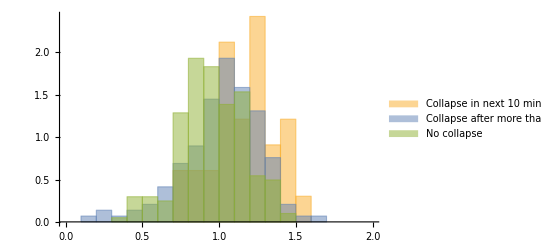

```mathematica
Histogram[{
Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],0<#[[2]]<4 10&][[All,1]],
Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],#[[2]]>4 10&][[All,1]],
permanentEdgeTensionsDorsal
},
{0,2,0.1},
"PDF",
ChartLegends->{"Collapse in next 10 min","Collapse after more than 10 min","No collapse"}
]
```

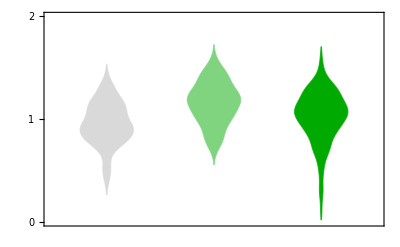

```mathematica
DistributionChart[{
Select[permanentEdgeTensionsDorsal,0<#<2&],
Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],0<#[[1]]<2&&0<#[[2]]<4 10&][[All,1]],
Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],0<#[[1]]<2&&#[[2]]>4 10&][[All,1]]
},
PlotRange->{0,2},
FrameTicks->{{{0,1,2},None},None},
ChartStyle->{LightGray,Blend[{Darker[Green],White},0.5],Darker[Green]}
]
```

```mathematica
Length/@{
Select[permanentEdgeTensionsDorsal,0<#<2&],
Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],0<#[[1]]<2&&0<#[[2]]<4 10&][[All,1]],
Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],0<#[[1]]<2&&#[[2]]>4 10&][[All,1]]
}
```

{202,33,145}

```mathematica
LocationTest[{
Select[permanentEdgeTensionsDorsal,0<#<2&],
Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],0<#[[1]]<2&&#[[2]]>4 10&][[All,1]]
},
0,
"T",
VerifyTestAssumptions->"EqualVariance"]
```

0.0075299

```mathematica
KolmogorovSmirnovTest[
Select[permanentEdgeTensionsDorsal,0<#<2&],
Select[Catenate[tensionCollapseTimeStratified[[7;;8]]],0<#[[1]]<2&&#[[2]]>4 10&][[All,1]]
]
```

0.0008409